```mathematica
x1=Import["/home/dk0r/git/comp-phys/HW_3/x-y_position.M1.csv"];
x2=Import["/home/dk0r/git/comp-phys/HW_3/x-y_position.M2.csv"];
```

```mathematica
m1 = ListPlot[x1];
m2=ListPlot[x2,PlotStyle->Red];
```

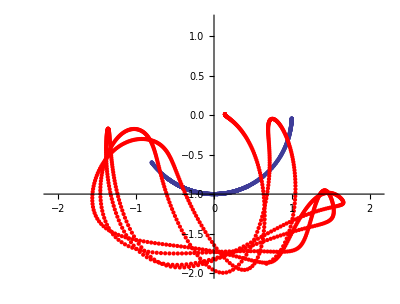

```mathematica
Show[m1,m2,PlotRange->{{-2.1,2.1},{-2,1.2}}, AspectRatio->Automatic]
```

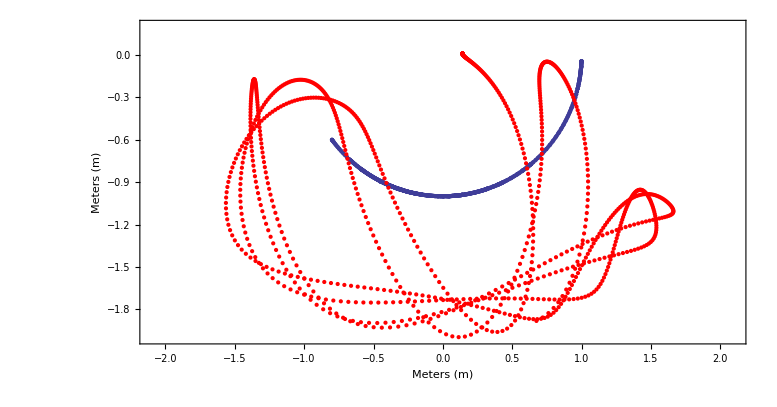

```mathematica
Show[m1,m2,PlotRange->{{-2.1,2.1},{-2,0.2}}, AspectRatio->Automatic, LabelStyle->{FontSize->15},Frame->True,FrameLabel->{"Meters (m)","Meters (m)"}]
```